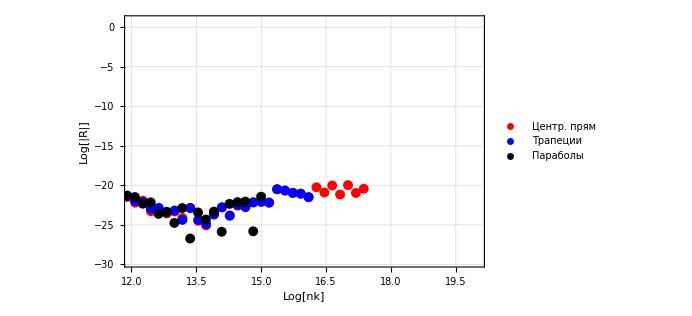

```mathematica
data={{1.3271,0.29664},{1.5094,-2.0529},{1.6917,-3.4063},{1.874,-2.4566},{2.0563,-2.5567},{2.2387,-2.5714},{2.421,-5.1265},{2.6033,-2.9587},{2.7856,-3.8225},{2.9679,-3.6127},{3.1503,-6.6778},{3.3326,-4.6986},{3.5149,-3.938},{3.6972,-5.8508},{3.8796,-6.2989},{4.0619,-6.253},{4.2442,-5.5302},{4.4265,-9.2815},{4.6088,-7.7321},{4.7912,-8.1936},{4.9735,-8.7287},{5.1558,-10.742},{5.3381,-8.86},{5.5204,-8.1612},{5.7028,-11.841},{5.8851,-12.205},{6.0674,-12.57},{6.2497,-11.129},{6.4321,-11.144},{6.6144,-11.463},{6.7967,-13.756},{6.979,-14.395},{7.1613,-13.41},{7.3437,-13.203},{7.526,-13.069},{7.7083,-14.885},{7.8906,-13.223},{8.0729,-13.416},{8.2553,-15.065},{8.4376,-15.092},{8.6199,-15.207},{8.8022,-14.895},{8.9846,-14.963},{9.1669,-17.578},{9.3492,-19.135},{9.5315,-19.5},{9.7138,-17.027},{9.8962,-17.91},{10.078,-17.122},{10.261,-20.958},{10.443,-21.333},{10.625,-19.44},{10.808,-22.075},{10.99,-19.505},{11.172,-21.807},{11.355,-22.866},{11.537,-22.27},{11.719,-21.205},{11.902,-21.477},{12.084,-22.188},{12.266,-21.951},{12.449,-23.27},{12.631,-23.045},{12.813,-23.555},{12.996,-23.312},{13.178,-24.137},{13.36,-22.841},{13.543,-24.487},{13.725,-25.064},{13.907,-23.667},{14.09,-22.791},{14.272,-23.823},{14.454,-22.532},{14.637,-22.741},{14.819,-22.152},{15.001,-22.087},{15.183,-22.186},{15.366,-20.494},{15.548,-20.659},{15.73,-20.955},{15.913,-21.059},{16.095,-21.498},{16.277,-20.254},{16.46,-20.908},{16.642,-20.021},{16.824,-21.165},{17.007,-19.97},{17.189,-20.963},{17.371,-20.434}
};
data1={
{1.3271,0.81473},{1.5094,-1.9971},{1.6917,-2.777},{1.874,-1.8528},{2.0563,-2.0652},{2.2387,-2.8156},{2.421,-4.4281},{2.6033,-2.7097},{2.7856,-4.234},{2.9679,-3.3996},{3.1503,-5.9835},{3.3326,-5.0223},{3.5149,-3.8363},{3.6972,-6.3838},{3.8796,-5.9099},{4.0619,-6.6109},{4.2442,-5.426},{4.4265,-8.5883},{4.6088,-8.3089},{4.7912,-7.7926},{4.9735,-8.2698},{5.1558,-10.049},{5.3381,-9.2395},{5.5204,-8.0556},{5.7028,-11.147},{5.8851,-11.512},{6.0674,-11.877},{6.2497,-10.727},{6.4321,-11.569},{6.6144,-11.176},{6.7967,-12.567},{6.979,-13.702},{7.1613,-14.913},{7.3437,-13.782},{7.526,-12.832},{7.7083,-14.124},{7.8906,-13.386},{8.0729,-13.297},{8.2553,-14.689},{8.4376,-15.485},{8.6199,-14.981},{8.8022,-15.033},{8.9846,-14.871},{9.1669,-19.986},{9.3492,-18.442},{9.5315,-18.807},{9.7138,-17.221},{9.8962,-17.651},{10.078,-17.033},{10.261,-20.266},{10.443,-20.626},{10.625,-19.821},{10.808,-21.349},{10.99,-19.354},{11.172,-23.828},{11.355,-21.683},{11.537,-24.284},{11.719,-21.437},{11.902,-21.303},{12.084,-21.952},{12.266,-22.11},{12.449,-22.948},{12.631,-22.853},{12.813,-23.337},{12.996,-23.185},{13.178,-24.371},{13.36,-22.881},{13.543,-24.357},{13.725,-24.886},{13.907,-23.695},{14.09,-22.781},{14.272,-23.838},{14.454,-22.535},{14.637,-22.744},{14.819,-22.151},{15.001,-22.088},{15.183,-22.186},{15.366,-20.493},{15.548,-20.659},{15.73,-20.955},{15.913,-21.059},{16.095,-21.498}
};
data2={
{4.7875,-6.3347},{4.9698,-7.0661},{5.1521,-7.0941},{5.3345,-8.8419},{5.5168,-8.7395},{5.6991,-10.643},{5.8814,-10.35},{6.0637,-9.6589},{6.2461,-26.328},{6.4284,-10.369},{6.6107,-27.6},{6.793,-10.482},{6.9754,-12.622},{7.1577,-29.486},{7.34,-14.348},{7.5223,-14.449},{7.7046,-14.698},{7.887,-14.389},{8.0693,-13.78},{8.2516,-28.161},{8.4339,-15.862},{8.6162,-16.002},{8.7986,-16.659},{8.9809,-27.315},{9.1632,-29.717},{9.3455,-29.221},{9.5279,-16.705},{9.7102,-16.551},{9.8925,-28.039},{10.075,-18.068},{10.257,-18.311},{10.439,-19.019},{10.622,-18.589},{10.804,-20.255},{10.986,-19.66},{11.169,-19.959},{11.351,-20.882},{11.533,-20.734},{11.716,-21.526},{11.898,-21.32},{12.08,-21.486},{12.263,-22.324},{12.445,-22.157},{12.627,-23.607},{12.81,-23.414},{12.992,-24.756},{13.174,-22.876},{13.357,-26.723},{13.539,-23.432},{13.721,-24.326},{13.904,-23.326},{14.086,-25.868},{14.268,-22.345},{14.451,-22.123},{14.633,-22.058},{14.815,-25.812},{14.997,-21.44}
};

Show[ListPlot[{data,data1,data2},
PlotStyle->{Red,Blue,Black},PlotLegends->Placed[
{Style["Центр. прям",20,Black,FontFamily->"Cambria"],
Style["Трапеции",20,Black,FontFamily->"Cambria"],
Style["Параболы",20,Black,FontFamily->"Cambria"]},Right]],
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["Log[nk]",20,Black,FontFamily->"Cambria"],Style["Log[|R|]",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512,
PlotRange->{{12,20},Automatic}
]
```

```mathematica
Clear[func, Rez,x]

f[t_]:=(t*Sin[t])/(1+(Cos[t])^2);

Clear[x];
Rez=0;
I0={};
func1[dx_]:=Module[{x=0},
While[x<Pi,Rez=Rez+f[(2*t+dx)/2]*dx/.{t->x};x+=dx]];
func2[dx_]:=Module[{x=0},
While[x<Pi,Rez=Rez+(f[t]+f[t+dx])/2*dx/.{t->x};x+=dx]];
func3[dx_]:=Module[{x=0},
While[x<Pi,Rez=Rez+(f[t]+f[t+dx]+4*f[(2*t+dx)/2])/6*dx/.{t->x};x+=dx]];
func1[Pi/10]
AppendTo[I0,Rez//N];
Rez=0;
func2[Pi/10]
AppendTo[I0,Rez//N];
Rez=0;
func3[Pi/10]
AppendTo[I0,Rez//N];
Rez=0;
I0
R=I0[[1]]/(4-1);
Rp=0;
Clear[dx];
dx = Pi/20;
I1=0;
Clear[LList1,LList2,LList3];
LList1={};
LList2={};
LList3={};
LList11={};
LList22={};
LList33={};
While[dx>Pi/5000,
dx=dx/2;
func1[dx];
I1=Rez//N;
Rp=R;
R=(I1-I0[[1]])/(4-1);
I0[[1]]=I1;
AppendTo[LList1,{Log[Pi/dx]//N,Log[Abs[Rp/R]]/Log[2]}];
AppendTo[LList11,{Log[Pi/dx]//N,Log[Abs[R]]}];
Rez=0
]
```

{2.47382,2.45452,2.46739}

```mathematica
Rez=0;
R=I0[[2]]/(4-1);
Rp=0;
Clear[dx];
dx = Pi/20;
I1=0;
While[dx>Pi/1000,
dx=dx/2;
func2[dx];
I1=Rez//N;
Rp=R;
R=(I1-I0[[2]])/(4-1);
I0[[2]]=I1;
AppendTo[LList2,{Log[Pi/dx]//N,Log[Abs[Rp/R]]/Log[2]}];
AppendTo[LList22,{Log[Pi/dx]//N,Log[Abs[R]]}];
Rez=0
]
```

```mathematica
Rez=0;
R=I0[[3]]/(16-1);
Rp=0;
Clear[dx];
dx = Pi/20;
I1=0;
While[dx>Pi/1000,
dx=dx/2;
func3[dx];
I1=Rez//N;
Rp=R;
R=(I1-I0[[3]])/(16-1);
I0[[3]]=I1;
AppendTo[LList3,{Log[Pi/dx]//N,Log[Abs[Rp/R]]/Log[2]}];
AppendTo[LList33,{Log[Pi/dx]//N,Log[Abs[R]]}];
Rez=0
]
```

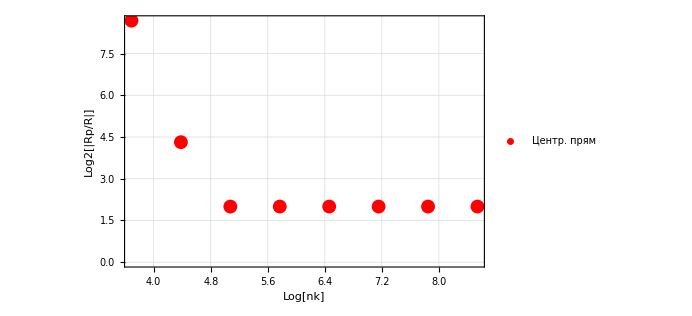

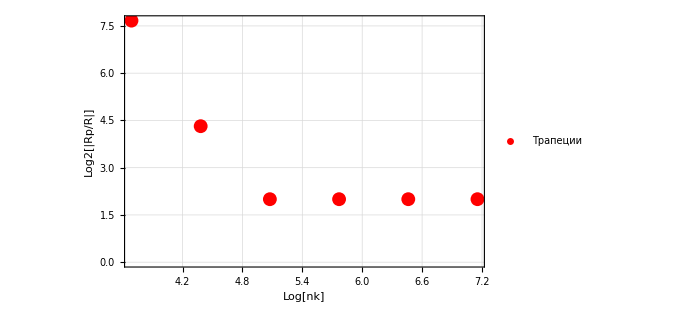

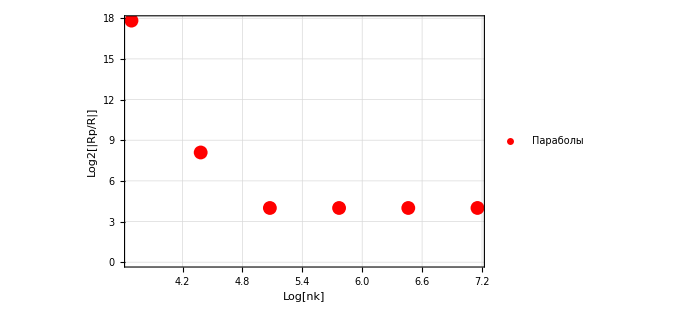

```mathematica
ListPlot[{LList1},PlotStyle->{Red,Blue,Black},PlotLegends->Placed[
{Style["Центр. прям",20,Black,FontFamily->"Cambria"]},Right],
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["Log[nk]",20,Black,FontFamily->"Cambria"],Style["Log2[|Rp/R|]",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512]
ListPlot[{LList2},PlotStyle->{Red,Blue,Black},PlotLegends->Placed[
{Style["Трапеции",20,Black,FontFamily->"Cambria"]},Right],
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["Log[nk]",20,Black,FontFamily->"Cambria"],Style["Log2[|Rp/R|]",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512]
ListPlot[{LList3},PlotStyle->{Red,Blue,Black},PlotLegends->Placed[
{Style["Параболы",20,Black,FontFamily->"Cambria"]},Right],
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["Log[nk]",20,Black,FontFamily->"Cambria"],Style["Log2[|Rp/R|]",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512]
```

{a→-2.04844}

{a→-1.92286}

{a→-4.33806}

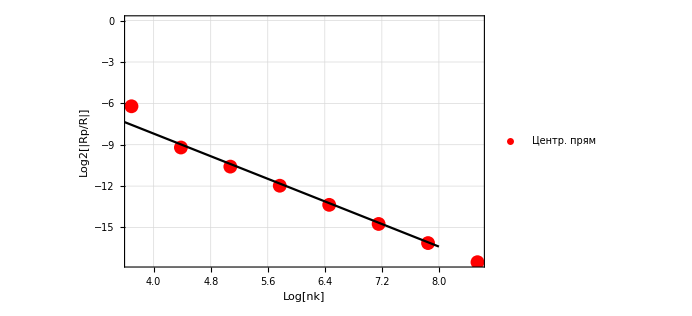

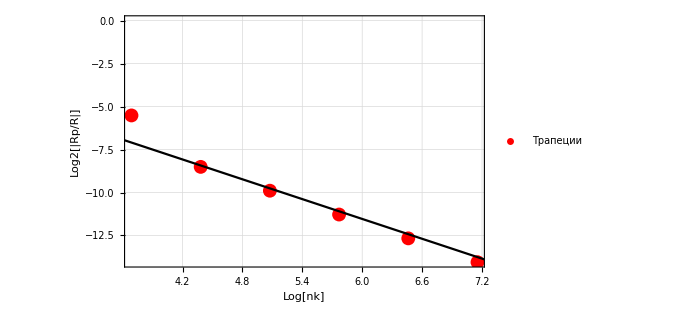

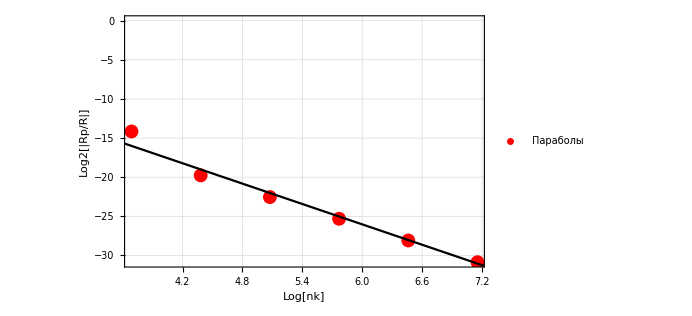

```mathematica
fit1=FindFit[LList11,a*x,a,x]
fit2=FindFit[LList22,a*x,a,x]
fit3=FindFit[LList33,a*x,a,x]
stl={
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["Log[nk]",20,Black,FontFamily->"Cambria"],Style["Log2[|Rp/R|]",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512
};
Show[ListPlot[{LList11},PlotStyle->Red,PlotLegends->Placed[
{Style["Центр. прям",20,Black,FontFamily->"Cambria"]},Right]],Plot[a*x/.{fit1},{x,3,10},PlotStyle->Black],stl]
Show[ListPlot[{LList22},PlotStyle->Red,PlotLegends->Placed[
{Style["Трапеции",20,Black,FontFamily->"Cambria"]},Right]],Plot[a*x/.{fit2},{x,3,8},PlotStyle->Black],stl]
Show[ListPlot[{LList33},PlotStyle->Red,PlotLegends->Placed[
{Style["Параболы",20,Black,FontFamily->"Cambria"]},Right]],Plot[a*x/.{fit3},{x,3,8},PlotStyle->Black],stl]
```

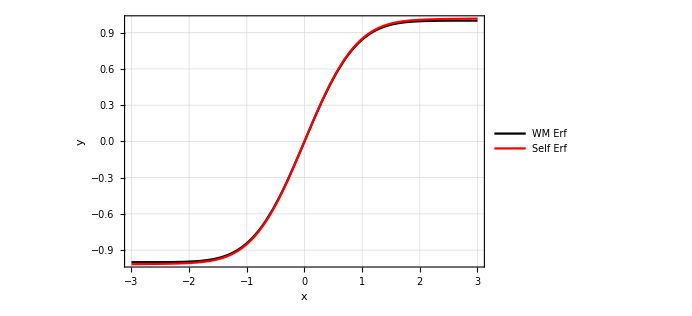

```mathematica
SERF[x_]:=2/(√Pi)*Sum[(E^(-t^2))*Abs[x]/100//N,{t,0,Abs[x],Abs[x]/100}]
stl={
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{Style["x",20,Black,FontFamily->"Cambria"],Style["y",20,Black,FontFamily->"Cambria"]},GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],ImageSize->512
};
Show[Plot[Erf[x],{x,-3,3},PlotStyle->Black,PlotLegends->Placed[
{Style["WM Erf",20,Black,FontFamily->"Cambria"]},Right]],
Plot[SERF[x],{x,0,3},PlotStyle->Red],Plot[-SERF[x],{x,-3,0},PlotStyle->Red,PlotLegends->Placed[
{Style["Self Erf",20,Black,FontFamily->"Cambria"]},Right]],stl]
```